## Two-stage SP:

```mathematica
<<Calendar`
(* Definition of functions to work on simulation part. *)
wData = Import["wt_data.csv","CSV",Path->NotebookDirectory[],"HeaderLines"->1];
solarRadi = Import["solar.txt","Table",Path-> NotebookDirectory[]];
markovChainMatrix = {{0.7,0.2,0.1},{0.6,0.3,0.1},{0.5,0.4,0.1}};
stateProb = markovChainMatrix[[1]].MatrixPower[markovChainMatrix,10];
randomStateSequence = RandomChoice[stateProb->{"N","A","M"},Dimensions[wData][[1]]];

(* Extract wind and time data *)
windSpeed = wData[[All,20]]/10*0.44704;
coolingDegreeHours = (wData[[All,2]]/.-7777->0)/10;
heatDegreeHours = (wData[[All,3]]/.-7777->0)/10;
cloudOvercastPercentage = ((wData[[All,3]])/.-7777->0)/10/100;
year[t_]:=(
DateString[{wData[[t,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Year"]//ToExpression
);
month[t_]:=(
DateString[{wData[[t,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Month"]//ToExpression
);
day[t_]:=(
DateString[{wData[[t,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Day"]//ToExpression
);
dayOfWeek[t_]:=(
DayOfWeek[{year[t],month[t],day[t]}]
);
(* Define Price of buying and selling. *)
BuyPrice[t_]:= (
If[MemberQ[{Saturday,Sunday},dayOfWeek[t]],0.051,
If[7≤ Mod[t,24]<11||17<Mod[t,24]≤ 21,0.099,
If[11≤Mod[t,24]≤ 17,0.081,
0.051
]
]
]
);
SellPrice[t_]:= 0.8*BuyPrice[t];

(* Initialize stages, currently two stages. *)
stageSize = 2;
availableResources = Table[0, {i,stageSize}];
demand = Table[0,{i, stageSize}];

(* Initial values to parameters. *)
airDensity = 1.27;
windTurbineCoefficientFactor = 0.5;
windTurbineRadius = 5;
solarRadiationFactor = 1.2;
solarPanelSize = 100;
initBatt =100;
t=15;
capBat=1000;

(* Function of Available Resources at time t: electricity power from wind energy and solar energy *)
AvailableResource[t_]:=(
0.5*windTurbineCoefficientFactor*windTurbineRadius^2*airDensity*Pi*windSpeed[[t]]^3+solarRadiationFactor*solarPanelSize*solarRadi[[Mod[t,24]+1,month[t]]]*(1-cloudOvercastPercentage[[t]])
);
(* Function of Local Demand at time t: pick a random integer from 1000 to 10000 *)
Demand[t_]:=(
(*If[t==18,100000,AvailableResource[t]+1000]*)
pLossRate = 1000;
heatDegreeHours[[t]]*pLossRate+coolingDegreeHours[[t]]*pLossRate+RandomInteger[{500,5000}]
(*RandomInteger[{1000,10000}]*)
);
(* Function of unit cost of reserving electricity in battery : set it constant *)
ReserveCost[t_]:=(0.02);
(* Function of unit cost of transiting electricity to or from battery : set it constant *)
TransitionCost[t_]:=(0.01);

(* Function of optimization of simple two-stage *)
(* 
	B->C:1,
	B->G:2,
	G->B:3,
	G->C:4,
	R->B:5,
	R->C:6,
	R->G:7
*)

StageMinimize[t_,initBatt_]:=(
Minimize[
{
(x[3]+x[4])*BuyPrice[t]+
(initBatt+x[3]+x[5]-x[1]-x[2])*ReserveCost[t] + 
(initBatt+x[3]+x[5]+x[1]+x[2])*TransitionCost[t]-
(x[2]+x[7])*SellPrice[t]+

If[randomStateSequence[[t]]=="N",markovChainMatrix[[1,1]],
If[randomStateSequence[[t]]=="A",markovChainMatrix[[2,1]],
markovChainMatrix[[3,1]]]]*(
	(y[3,1]+y[4,1])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]-y[1,1]-y[2,1])*ReserveCost[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]+y[1,1]+y[2,1])*TransitionCost[t+1]-
	(y[2,1]+y[7,1])*SellPrice[t+1])+

If[randomStateSequence[[t]]=="N",markovChainMatrix[[1,2]],
If[randomStateSequence[[t]]=="A",markovChainMatrix[[2,2]],
markovChainMatrix[3,2]]]*(
	(y[3,2]+y[4,2])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]-y[1,2]-y[2,2])*ReserveCost[t+1]+  
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]+y[1,2]+y[2,2])*TransitionCost[t+1]-
		(y[2,2]+y[7,2])*SellPrice[t+1])+

If[randomStateSequence[[t]]=="N",markovChainMatrix[[1,3]],
If[randomStateSequence[[t]]=="A",markovChainMatrix[[2,3]],
markovChainMatrix[[3,3]]]]*(
	(y[3,3]+y[4,3])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]-y[1,3]-y[2,3])*ReserveCost[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]+y[1,3]+y[2,3])*TransitionCost[t+1]-
	(y[2,3]+y[7,3])*SellPrice[t+1]),

x[1]+x[4]+x[6]==Demand[t]&&
0≤ initBatt+x[5]+x[3]-x[2]-x[1]≤ capBat&&
x[7]+x[5]+x[6]==AvailableResource[t]&&
x[3]≥0&&x[4]≥0&&x[5]≥0&&x[6]≥0&&x[7]≥0&&x[1]≥0&&x[2]≥0&&

y[1,1]+y[4,1]+y[6,1]==Demand[t+1]&&
-(initBatt+x[3]+x[5]-x[1]-x[2])≤ y[5,1]+y[3,1]-y[2,1]-y[1,1]≤ capBat-(initBatt+x[3]+x[5]-x[1]-x[2])&&
y[7,1]+y[5,1]+y[6,1]==AvailableResource[t+1]&&
y[3,1]≥0&&y[4,1]≥0&&y[5,1]≥0&&y[6,1]≥0&&y[7,1]≥0&&y[1,1]≥0&&y[2,1]≥0&&

y[1,2]+y[4,2]+y[6,2]==Demand[t+1]&&
-(initBatt+x[3]+x[5]-x[1]-x[2])≤ y[5,2]+y[3,2]-y[2,2]-y[1,2]≤ capBat-(initBatt+x[3]+x[5]-x[1]-x[2])&&
y[7,2]+y[5,2]+y[6,2]==AvailableResource[t+1]/2&&
y[3,2]≥0&&y[4,2]≥0&&y[5,2]≥0&&y[6,2]≥0&&y[7,2]≥0&&y[1,2]≥0&&y[2,2]≥0&&

y[1,3]+y[4,3]+y[6,3]==Demand[t+1]&&
-(initBatt+x[3]+x[5]-x[1]-x[2])≤ y[5,3]+y[3,3]-y[2,3]-y[1,3]≤ capBat-(initBatt+x[3]+x[5]-x[1]-x[2])&&
y[7,3]+y[5,3]+y[6,3]==AvailableResource[t+1]/4&&
y[3,3]≥0&&y[4,3]≥0&&y[5,3]≥0&&y[6,3]≥0&&y[7,3]≥0&&y[1,3]≥0&&y[2,3]≥0
},
{x[3],x[4],x[5],x[6],x[7],x[1],x[2],y[3,1],y[4,1],y[5,1],y[6,1],y[7,1],y[1,1],y[2,1],y[3,2],y[4,2],y[5,2],y[6,2],y[7,2],y[1,2],y[2,2],y[3,3],y[4,3],y[5,3],y[6,3],y[7,3],y[1,3],y[2,3]}]
);
```

```mathematica
firstStage = StageMinimize[t,initBatt]
```

{4872.06,{x[3]→0.,x[4]→28097.4,x[5]→0.,x[6]→11649.6,x[7]→0.,x[1]→100.,x[2]→0.,y[3,1]→0.,y[4,1]→30776.1,y[5,1]→0.,y[6,1]→4939.93,y[7,1]→0.,y[1,1]→0.,y[2,1]→0.,y[3,2]→0.,y[4,2]→34817.,y[5,2]→0.,y[6,2]→2469.96,y[7,2]→0.,y[1,2]→0.,y[2,2]→0.,y[3,3]→0.,y[4,3]→35201.,y[5,3]→0.,y[6,3]→1234.98,y[7,3]→0.,y[1,3]→0.,y[2,3]→0.}}

## Three stages SP:

```mathematica
<<Calendar`
(* Definition of functions to work on simulation part. *)
wData = Import["wt_data.csv","CSV",Path->NotebookDirectory[],"HeaderLines"->1];
solarRadi = Import["solar.txt","Table",Path-> NotebookDirectory[]];
markovChainMatrix = {{0.7,0.2,0.1},{0.6,0.3,0.1},{0.5,0.4,0.1}};

(* Three-stage probability matrix *)
t1= Flatten[DiagonalMatrix[markovChainMatrix[[1,All]]].markovChainMatrix];
t2= Flatten[DiagonalMatrix[markovChainMatrix[[2,All]]].markovChainMatrix];
t3= Flatten[DiagonalMatrix[markovChainMatrix[[3,All]]].markovChainMatrix];
threeMatrix = {t1,t2,t3};

stateProb = markovChainMatrix[[1]].MatrixPower[markovChainMatrix,10];
randomStateSequence = RandomChoice[stateProb->{"N","A","M"},Dimensions[wData][[1]]];

(* Extract wind and time data *)
windSpeed = wData[[All,20]]/10*0.44704;
coolingDegreeHours = (wData[[All,2]]/.-7777->0)/10;
heatDegreeHours = (wData[[All,3]]/.-7777->0)/10;
cloudOvercastPercentage = ((wData[[All,3]])/.-7777->0)/10/100;
year[t_]:=(
DateString[{wData[[t,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Year"]//ToExpression
);
month[t_]:=(
DateString[{wData[[t,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Month"]//ToExpression
);
day[t_]:=(
DateString[{wData[[t,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Day"]//ToExpression
);
dayOfWeek[t_]:=(
DayOfWeek[{year[t],month[t],day[t]}]
);
(* Define Price of buying and selling. *)
BuyPrice[t_]:= (
If[MemberQ[{Saturday,Sunday},dayOfWeek[t]],0.051,
If[7≤ Mod[t,24]<11||17<Mod[t,24]≤ 21,0.099,
If[11≤Mod[t,24]≤ 17,0.081,
0.051
]
]
]
);
SellPrice[t_]:= 0.8*BuyPrice[t];

(* Initialize stages, currently two stages. *)
stageSize = 2;
availableResources = Table[0, {i,stageSize}];
demand = Table[0,{i, stageSize}];

(* Initial values to parameters. *)
airDensity = 1.27;
windTurbineCoefficientFactor = 0.5;
windTurbineRadius = 5;
solarRadiationFactor = 1.2;
solarPanelSize = 100;
initBatt =100;
t=15;
capBat=1000;

(* Function of Available Resources at time t: electricity power from wind energy and solar energy *)
AvailableResource[t_]:=(
0.5*windTurbineCoefficientFactor*windTurbineRadius^2*airDensity*Pi*windSpeed[[t]]^3+solarRadiationFactor*solarPanelSize*solarRadi[[Mod[t,24]+1,month[t]]]*(1-cloudOvercastPercentage[[t]])
);
(* Function of Local Demand at time t: pick a random integer from 1000 to 10000 *)
Demand[t_]:=(
(*If[t==18,100000,AvailableResource[t]+1000]*)
pLossRate = 1000;
heatDegreeHours[[t]]*pLossRate+coolingDegreeHours[[t]]*pLossRate+RandomInteger[{500,5000}]
(*RandomInteger[{1000,10000}]*)
);
(* Function of unit cost of reserving electricity in battery : set it constant *)
ReserveCost[t_]:=(0.02);
(* Function of unit cost of transiting electricity to or from battery : set it constant *)
TransitionCost[t_]:=(0.01);

(* Function of optimization of simple two-stage *)
(* 
	B->C:1,
	B->G:2,
	G->B:3,
	G->C:4,
	R->B:5,
	R->C:6,
	R->G:7
*)
StageMinimize[t_,initBatt_]:=(
Minimize[{x[2],
y[1,3]+y[4,3]+y[6,3]==Demand[t+1]&&
-(initBatt+x[3]+x[5]-x[1]-x[2])≤ y[5,3]+y[3,3]-y[2,3]-y[1,3]≤ capBat-(initBatt+x[3]+x[5]-x[1]-x[2])&&
y[7,3]+y[5,3]+y[6,3]==AvailableResource[t+1]/4&&
y[3,3]≥0&&y[4,3]≥0&&y[5,3]≥0&&y[6,3]≥0&&y[7,3]≥0&&y[1,3]≥0&&y[2,3]≥0&&

(*state[t+2]*)
z[1,1]+z[4,1]+z[6,1]==Demand[t+2]&&
-(initBatt+x[3]+x[5]-x[1]-x[2])≤ y[5,1]+y[3,1]-y[2,1]-y[1,1]≤ capBat-(initBatt+x[3]+x[5]-x[1]-x[2])&&
y[7,1]+y[5,1]+y[6,1]==AvailableResource[t+1]
&&z[1,1]≥0&&z[1,2]≥0&&z[1,3]≥0&&z[1,4]≥0&&z[1,5]≥0&&z[1,6]≥0&&z[1,7]≥0&&z[1,8]≥0&&z[1,9]≥0
&&z[2,1]≥0&&z[2,2]≥0&&z[2,3]≥0&&z[2,4]≥0&&z[2,5]≥0&&z[2,6]≥0&&z[2,7]≥0&&z[2,8]≥0&&z[2,9]≥0
&&z[3,1]≥0&&z[3,2]≥0&&z[3,3]≥0&&z[3,4]≥0&&z[3,5]≥0&&z[3,6]≥0&&z[3,7]≥0&&z[3,8]≥0&&z[3,9]≥0
&&z[4,1]≥0&&z[4,2]≥0&&z[4,3]≥0&&z[4,4]≥0&&z[4,5]≥0&&z[4,6]≥0&&z[4,7]≥0&&z[4,8]≥0&&z[4,9]≥0
&&z[5,1]≥0&&z[5,2]≥0&&z[5,3]≥0&&z[5,4]≥0&&z[5,5]≥0&&z[5,6]≥0&&z[5,7]≥0&&z[5,8]≥0&&z[5,9]≥0
&&z[6,1]≥0&&z[6,2]≥0&&z[6,3]≥0&&z[6,4]≥0&&z[6,5]≥0&&z[6,6]≥0&&z[6,7]≥0&&z[6,8]≥0&&z[6,9]≥0
&&z[7,1]≥0&&z[7,2]≥0&&z[7,3]≥0&&z[7,4]≥0&&z[7,5]≥0&&z[7,6]≥0&&z[7,7]≥0&&z[7,8]≥0&&z[7,9]≥0
},
{x[3],x[4],x[5],x[6],x[7],x[1],x[2],
y[3,1],y[4,1],y[5,1],y[6,1],y[7,1],y[1,1],y[2,1],y[3,2],y[4,2],y[5,2],y[6,2],y[7,2],y[1,2],y[2,2],y[3,3],y[4,3],y[5,3],y[6,3],y[7,3],y[1,3],y[2,3],
z[1,1],z[2,1],z[3,1],z[4,1],z[5,1],z[6,1],z[7,1],
z[1,2],z[2,2],z[3,2],z[4,2],z[5,2],z[6,2],z[7,2],
z[1,3],z[2,3],z[3,3],z[4,3],z[5,3],z[6,3],z[7,3],
z[1,4],z[2,4],z[3,4],z[4,4],z[5,4],z[6,4],z[7,4],
z[1,5],z[2,5],z[3,5],z[4,5],z[5,5],z[6,5],z[7,5],
z[1,6],z[2,6],z[3,6],z[4,6],z[5,6],z[6,6],z[7,6],
z[1,7],z[2,7],z[3,7],z[4,7],z[5,7],z[6,7],z[7,7],
z[1,8],z[2,8],z[3,8],z[4,8],z[5,8],z[6,8],z[7,8],
z[1,9],z[2,9],z[3,9],z[4,9],z[5,9],z[6,9],z[7,9]}]
);
```

```mathematica
firstStep = StageMinimize[10,10]
```

## New Three-stage SP:

```mathematica
<<Calendar`
(* Definition of functions to work on simulation part. *)
wData = Import["wt_data.csv","CSV",Path->NotebookDirectory[],"HeaderLines"->1];
solarRadi = Import["solar.txt","Table",Path-> NotebookDirectory[]];
markovChainMatrix = {{0.7,0.2,0.1},{0.6,0.3,0.1},{0.5,0.4,0.1}};

(* Three-stage probability matrix *)
t1= Flatten[DiagonalMatrix[markovChainMatrix[[1,All]]].markovChainMatrix];
t2= Flatten[DiagonalMatrix[markovChainMatrix[[2,All]]].markovChainMatrix];
t3= Flatten[DiagonalMatrix[markovChainMatrix[[3,All]]].markovChainMatrix];
threeMatrix = {t1,t2,t3};

stateProb = markovChainMatrix[[1]].MatrixPower[markovChainMatrix,10];
randomStateSequence = RandomChoice[stateProb->{"N","A","M"},Dimensions[wData][[1]]];

(* Extract wind and time data *)
windSpeed = wData[[All,20]]/10*0.44704;
coolingDegreeHours = (wData[[All,2]]/.-7777->0)/10;
heatDegreeHours = (wData[[All,3]]/.-7777->0)/10;
cloudOvercastPercentage = ((wData[[All,3]])/.-7777->0)/10/100;
year[t_]:=(
DateString[{wData[[t,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Year"]//ToExpression
);
month[t_]:=(
DateString[{wData[[t,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Month"]//ToExpression
);
day[t_]:=(
DateString[{wData[[t,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Day"]//ToExpression
);
dayOfWeek[t_]:=(
DayOfWeek[{year[t],month[t],day[t]}]
);
(* Define Price of buying and selling. *)
BuyPrice[t_]:= (
If[MemberQ[{Saturday,Sunday},dayOfWeek[t]],0.051,
If[7≤ Mod[t,24]<11||17<Mod[t,24]≤ 21,0.099,
If[11≤Mod[t,24]≤ 17,0.081,
0.051
]
]
]
);
SellPrice[t_]:= 0.8*BuyPrice[t];

(* Initialize stages, currently two stages. *)
stageSize = 2;
availableResources = Table[0, {i,stageSize}];
demand = Table[0,{i, stageSize}];

(* Initial values to parameters. *)
airDensity = 1.27;
windTurbineCoefficientFactor = 0.5;
windTurbineRadius = 5;
solarRadiationFactor = 1.2;
solarPanelSize = 100;
initBatt =100;
t=15;
capBat=1000;

(* Function of Available Resources at time t: electricity power from wind energy and solar energy *)
AvailableResource[t_]:=(
0.5*windTurbineCoefficientFactor*windTurbineRadius^2*airDensity*Pi*windSpeed[[t]]^3+solarRadiationFactor*solarPanelSize*solarRadi[[Mod[t,24]+1,month[t]]]*(1-cloudOvercastPercentage[[t]])
);
(* Function of Local Demand at time t: pick a random integer from 1000 to 10000 *)
Demand[t_]:=(
(*If[t==18,100000,AvailableResource[t]+1000]*)
pLossRate = 1000;
heatDegreeHours[[t]]*pLossRate+coolingDegreeHours[[t]]*pLossRate+RandomInteger[{500,5000}]
(*RandomInteger[{1000,10000}]*)
);
(* Function of unit cost of reserving electricity in battery : set it constant *)
ReserveCost[t_]:=(0.002);
(* Function of unit cost of transiting electricity to or from battery : set it constant *)
TransitionCost[t_]:=(0.001);

(* Function of optimization of simple two-stage *)
(* 
	B->C:1,
	B->G:2,
	G->B:3,
	G->C:4,
	R->B:5,
	R->C:6,
	R->G:7
*)
StageMinimize[t_,initBatt_]:=(
Minimize[
{
(x[3]+x[4])*BuyPrice[t]+
(initBatt+x[3]+x[5]-x[1]-x[2])*ReserveCost[t] + 
(initBatt+x[3]+x[5]+x[1]+x[2])*TransitionCost[t]-
(x[2]+x[7])*SellPrice[t]+

(*Stage[t+2]*)
If[randomStateSequence[[t]]=="N",threeMatrix[[1,1]],
If[randomStateSequence[[t]]=="A",threeMatrix[[2,1]],
threeMatrix[[3,1]]]]*(
(y[3,1]+y[4,1])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]-y[1,1]-y[2,1])*ReserveCost[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]+y[1,1]+y[2,1])*TransitionCost[t+1]-
	(y[2,1]+y[7,1])*SellPrice[t+1]+

	(z[3,1]+z[4,1])*BuyPrice[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]-y[1,1]-y[2,1]+z[3,1]+z[5,1]-z[1,1]-z[2,1])*ReserveCost[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]+y[1,1]+y[2,1]+z[3,1]+z[5,1]+z[1,1]+z[2,1])*TransitionCost[t+2]-
	(z[2,1]+z[7,1])*SellPrice[t+2])+

If[randomStateSequence[[t]]=="N",threeMatrix[[1,2]],
If[randomStateSequence[[t]]=="A",threeMatrix[[2,2]],
threeMatrix[3,2]]]*(
(y[3,2]+y[4,2])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]-y[1,2]-y[2,2])*ReserveCost[t+1]+  
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]+y[1,2]+y[2,2])*TransitionCost[t+1]-
		(y[2,2]+y[7,2])*SellPrice[t+1]+

	(z[3,2]+z[4,2])*BuyPrice[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]-y[1,2]-y[2,2]+z[3,2]+z[5,2]-z[1,2]-z[2,2])*ReserveCost[t+2]+  
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]+y[1,2]+y[2,2]+z[3,2]+z[5,2]+z[1,2]+z[2,2])*TransitionCost[t+2]-
	(z[2,2]+z[7,2])*SellPrice[t+2])+

If[randomStateSequence[[t]]=="N",threeMatrix[[1,3]],
If[randomStateSequence[[t]]=="A",threeMatrix[[2,3]],
threeMatrix[[3,3]]]]*(
(y[3,3]+y[4,3])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]-y[1,3]-y[2,3])*ReserveCost[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]+y[1,3]+y[2,3])*TransitionCost[t+1]-
	(y[2,3]+y[7,3])*SellPrice[t+1]+

	(z[3,3]+z[4,3])*BuyPrice[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]-y[1,3]-y[2,3]+z[3,3]+z[5,3]-z[1,3]-z[2,3])*ReserveCost[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]+y[1,3]+y[2,3]+z[3,3]+z[5,3]+z[1,3]+z[2,3])*TransitionCost[t+2]-
	(z[2,3]+z[7,3])*SellPrice[t+2])+

If[randomStateSequence[[t]]=="N",threeMatrix[[1,4]],
If[randomStateSequence[[t]]=="A",threeMatrix[[2,4]],
threeMatrix[[3,4]]]]*(
	(y[3,1]+y[4,1])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]-y[1,1]-y[2,1])*ReserveCost[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]+y[1,1]+y[2,1])*TransitionCost[t+1]-
	(y[2,1]+y[7,1])*SellPrice[t+1]+

	(z[3,4]+z[4,4])*BuyPrice[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]-y[1,1]-y[2,1]+z[3,4]+z[5,4]-z[1,4]-z[2,4])*ReserveCost[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]+y[1,1]+y[2,1]+z[3,4]+z[5,4]+z[1,4]+z[2,4])*TransitionCost[t+2]-
	(z[2,4]+z[7,4])*SellPrice[t+2])+

If[randomStateSequence[[t]]=="N",threeMatrix[[1,5]],
If[randomStateSequence[[t]]=="A",threeMatrix[[2,5]],
threeMatrix[[3,5]]]]*(
(y[3,2]+y[4,2])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]-y[1,2]-y[2,2])*ReserveCost[t+1]+  
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]+y[1,2]+y[2,2])*TransitionCost[t+1]-
		(y[2,2]+y[7,2])*SellPrice[t+1]+

	(z[3,5]+z[4,5])*BuyPrice[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]-y[1,2]-y[2,2]+z[3,5]+z[5,5]-z[1,5]-z[2,5])*ReserveCost[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]+y[1,2]+y[2,2]+z[3,5]+z[5,5]+z[1,5]+z[2,5])*TransitionCost[t+2]-
	(z[2,5]+z[7,5])*SellPrice[t+2])+

If[randomStateSequence[[t]]=="N",threeMatrix[[1,6]],
If[randomStateSequence[[t]]=="A",threeMatrix[[2,6]],
threeMatrix[[3,6]]]]*(
(y[3,3]+y[4,3])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]-y[1,3]-y[2,3])*ReserveCost[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]+y[1,3]+y[2,3])*TransitionCost[t+1]-
	(y[2,3]+y[7,3])*SellPrice[t+1]+

	(z[3,6]+z[4,6])*BuyPrice[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]-y[1,3]-y[2,3]+z[3,6]+z[5,6]-z[1,6]-z[2,6])*ReserveCost[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]+y[1,3]+y[2,3]+z[3,6]+z[5,6]+z[1,6]+z[2,6])*TransitionCost[t+2]-
	(z[2,6]+z[7,6])*SellPrice[t+2])+

If[randomStateSequence[[t]]=="N",threeMatrix[[1,7]],
If[randomStateSequence[[t]]=="A",threeMatrix[[2,7]],
threeMatrix[[3,7]]]]*(
(y[3,1]+y[4,1])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]-y[1,1]-y[2,1])*ReserveCost[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]+y[1,1]+y[2,1])*TransitionCost[t+1]-
	(y[2,1]+y[7,1])*SellPrice[t+1]+

	(z[3,7]+z[4,7])*BuyPrice[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]-y[1,1]-y[2,1]+z[3,7]+z[5,7]-z[1,7]-z[2,7])*ReserveCost[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]+y[1,1]+y[2,1]+z[3,7]+z[5,7]+z[1,7]+z[2,7])*TransitionCost[t+2]-
	(z[2,7]+z[7,7])*SellPrice[t+2])+

If[randomStateSequence[[t]]=="N",threeMatrix[[1,8]],
If[randomStateSequence[[t]]=="A",threeMatrix[[2,8]],
threeMatrix[[3,8]]]]*(
	(y[3,2]+y[4,2])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]-y[1,2]-y[2,2])*ReserveCost[t+1]+  
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]+y[1,2]+y[2,2])*TransitionCost[t+1]-
		(y[2,2]+y[7,2])*SellPrice[t+1]+

	(z[3,8]+z[4,8])*BuyPrice[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]-y[1,2]-y[2,2]+z[3,8]+z[5,8]-z[1,8]-z[2,8])*ReserveCost[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]+y[1,2]+y[2,2]+z[3,8]+z[5,8]+z[1,8]+z[2,8])*TransitionCost[t+2]-
	(z[2,8]+z[7,8])*SellPrice[t+2])+

If[randomStateSequence[[t]]=="N",threeMatrix[[1,9]],
If[randomStateSequence[[t]]=="A",threeMatrix[[2,9]],
threeMatrix[[3,9]]]]*(
	(y[3,3]+y[4,3])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]-y[1,3]-y[2,3])*ReserveCost[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]+y[1,3]+y[2,3])*TransitionCost[t+1]-
	(y[2,3]+y[7,3])*SellPrice[t+1]+

	(z[3,9]+z[4,9])*BuyPrice[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]-y[1,3]-y[2,3]+z[3,9]+z[5,9]-z[1,9]-z[2,9])*ReserveCost[t+2]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]+y[1,3]+y[2,3]+z[3,9]+z[5,9]+z[1,9]+z[2,9])*TransitionCost[t+2]-
	(z[2,9]+z[7,9])*SellPrice[t+2]),

x[1]+x[4]+x[6]==Demand[t]&&
0≤ initBatt+x[5]+x[3]-x[2]-x[1]≤ capBat&&
x[7]+x[5]+x[6]==AvailableResource[t]&&
x[3]≥0&&x[4]≥0&&x[5]≥0&&x[6]≥0&&x[7]≥0&&x[1]≥0&&x[2]≥0&&

(*stage[t+1]*)
y[1,1]+y[4,1]+y[6,1]==Demand[t+1]&&
-(initBatt+x[3]+x[5]-x[1]-x[2])≤ y[5,1]+y[3,1]-y[2,1]-y[1,1]≤ capBat-(initBatt+x[3]+x[5]-x[1]-x[2])&&
y[7,1]+y[5,1]+y[6,1]==AvailableResource[t+1]&&
y[3,1]≥0&&y[4,1]≥0&&y[5,1]≥0&&y[6,1]≥0&&y[7,1]≥0&&y[1,1]≥0&&y[2,1]≥0&&

y[1,2]+y[4,2]+y[6,2]==Demand[t+1]&&
-(initBatt+x[3]+x[5]-x[1]-x[2])≤ y[5,2]+y[3,2]-y[2,2]-y[1,2]≤ capBat-(initBatt+x[3]+x[5]-x[1]-x[2])&&
y[7,2]+y[5,2]+y[6,2]==AvailableResource[t+1]/2&&
y[3,2]≥0&&y[4,2]≥0&&y[5,2]≥0&&y[6,2]≥0&&y[7,2]≥0&&y[1,2]≥0&&y[2,2]≥0&&

y[1,3]+y[4,3]+y[6,3]==Demand[t+1]&&
-(initBatt+x[3]+x[5]-x[1]-x[2])≤ y[5,3]+y[3,3]-y[2,3]-y[1,3]≤ capBat-(initBatt+x[3]+x[5]-x[1]-x[2])&&
y[7,3]+y[5,3]+y[6,3]==AvailableResource[t+1]/4&&
y[3,3]≥0&&y[4,3]≥0&&y[5,3]≥0&&y[6,3]≥0&&y[7,3]≥0&&y[1,3]≥0&&y[2,3]≥0&&

(*state[t+2]*)
z[1,1]+z[4,1]+z[6,1]==Demand[t+2]&&
0≤ (initBatt+x[3]+x[5]-x[1]-x[2])+y[5,1]+y[3,1]-y[2,1]-y[1,1]+z[5,1]+z[3,1]-z[2,1]-z[1,1]≤ capBat&&
z[7,1]+z[5,1]+z[6,1]==AvailableResource[t+2]&&

z[1,2]+z[4,2]+z[6,2]==Demand[t+2]&&
0≤ (initBatt+x[3]+x[5]-x[1]-x[2])+y[5,1]+y[3,1]-y[2,1]-y[1,1]+z[5,2]+z[3,2]-z[2,2]-z[1,2]≤ capBat&&
z[7,2]+z[5,2]+z[6,2]==AvailableResource[t+2]/2&&

z[1,3]+z[4,3]+z[6,3]==Demand[t+2]&&
0≤ (initBatt+x[3]+x[5]-x[1]-x[2])+y[5,1]+y[3,1]-y[2,1]-y[1,1]+z[5,3]+z[3,3]-z[2,3]-z[1,3]≤ capBat&&
z[7,3]+z[5,3]+z[6,3]==AvailableResource[t+2]/4&&

z[1,4]+z[4,4]+z[6,4]==Demand[t+2]&&
0≤ (initBatt+x[3]+x[5]-x[1]-x[2])+y[5,1]+y[3,1]-y[2,1]-y[1,1]+z[5,4]+z[3,4]-z[2,4]-z[1,4]≤ capBat&&
z[7,4]+z[5,4]+z[6,4]==AvailableResource[t+2]&&

z[1,5]+z[4,5]+z[6,5]==Demand[t+2]&&
0≤ (initBatt+x[3]+x[5]-x[1]-x[2])+y[5,1]+y[3,1]-y[2,1]-y[1,1]+z[5,5]+z[3,5]-z[2,5]-z[1,5]≤ capBat&&
z[7,5]+z[5,5]+z[6,5]==AvailableResource[t+2]/2&&

z[1,6]+z[4,6]+z[6,6]==Demand[t+2]&&
0≤ (initBatt+x[3]+x[5]-x[1]-x[2])+y[5,1]+y[3,1]-y[2,1]-y[1,1]+z[5,6]+z[3,6]-z[2,6]-z[1,6]≤ capBat&&
z[7,6]+z[5,6]+z[6,6]==AvailableResource[t+2]/4&&

z[1,7]+z[4,7]+z[6,7]==Demand[t+2]&&
0≤ (initBatt+x[3]+x[5]-x[1]-x[2])+y[5,1]+y[3,1]-y[2,1]-y[1,1]+z[5,7]+z[3,7]-z[2,7]-z[1,7]≤ capBat&&
z[7,7]+z[5,7]+z[6,7]==AvailableResource[t+2]&&

z[1,8]+z[4,8]+z[6,8]==Demand[t+2]&&
0≤ (initBatt+x[3]+x[5]-x[1]-x[2])+y[5,1]+y[3,1]-y[2,1]-y[1,1]+z[5,8]+z[3,8]-z[2,8]-z[1,8]≤ capBat&&
z[7,8]+z[5,8]+z[6,8]==AvailableResource[t+2]/2&&

z[1,9]+z[4,9]+z[6,9]==Demand[t+2]&&
0≤ (initBatt+x[3]+x[5]-x[1]-x[2])+y[5,1]+y[3,1]-y[2,1]-y[1,1]+z[5,9]+z[3,9]-z[2,9]-z[1,9]≤ capBat&&
z[7,9]+z[5,9]+z[6,9]==AvailableResource[t+2]/4
&&z[1,1]≥0&&z[1,2]≥0&&z[1,3]≥0&&z[1,4]≥0&&z[1,5]≥0&&z[1,6]≥0&&z[1,7]≥0&&z[1,8]≥0&&z[1,9]≥0
&&z[2,1]≥0&&z[2,2]≥0&&z[2,3]≥0&&z[2,4]≥0&&z[2,5]≥0&&z[2,6]≥0&&z[2,7]≥0&&z[2,8]≥0&&z[2,9]≥0
&&z[3,1]≥0&&z[3,2]≥0&&z[3,3]≥0&&z[3,4]≥0&&z[3,5]≥0&&z[3,6]≥0&&z[3,7]≥0&&z[3,8]≥0&&z[3,9]≥0
&&z[4,1]≥0&&z[4,2]≥0&&z[4,3]≥0&&z[4,4]≥0&&z[4,5]≥0&&z[4,6]≥0&&z[4,7]≥0&&z[4,8]≥0&&z[4,9]≥0
&&z[5,1]≥0&&z[5,2]≥0&&z[5,3]≥0&&z[5,4]≥0&&z[5,5]≥0&&z[5,6]≥0&&z[5,7]≥0&&z[5,8]≥0&&z[5,9]≥0
&&z[6,1]≥0&&z[6,2]≥0&&z[6,3]≥0&&z[6,4]≥0&&z[6,5]≥0&&z[6,6]≥0&&z[6,7]≥0&&z[6,8]≥0&&z[6,9]≥0
&&z[7,1]≥0&&z[7,2]≥0&&z[7,3]≥0&&z[7,4]≥0&&z[7,5]≥0&&z[7,6]≥0&&z[7,7]≥0&&z[7,8]≥0&&z[7,9]≥0
},
{x[3],x[4],x[5],x[6],x[7],x[1],x[2],
y[3,1],y[4,1],y[5,1],y[6,1],y[7,1],y[1,1],y[2,1],y[3,2],y[4,2],y[5,2],y[6,2],y[7,2],y[1,2],y[2,2],y[3,3],y[4,3],y[5,3],y[6,3],y[7,3],y[1,3],y[2,3],
z[1,1],z[2,1],z[3,1],z[4,1],z[5,1],z[6,1],z[7,1],
z[1,2],z[2,2],z[3,2],z[4,2],z[5,2],z[6,2],z[7,2],
z[1,3],z[2,3],z[3,3],z[4,3],z[5,3],z[6,3],z[7,3],
z[1,4],z[2,4],z[3,4],z[4,4],z[5,4],z[6,4],z[7,4],
z[1,5],z[2,5],z[3,5],z[4,5],z[5,5],z[6,5],z[7,5],
z[1,6],z[2,6],z[3,6],z[4,6],z[5,6],z[6,6],z[7,6],
z[1,7],z[2,7],z[3,7],z[4,7],z[5,7],z[6,7],z[7,7],
z[1,8],z[2,8],z[3,8],z[4,8],z[5,8],z[6,8],z[7,8],
z[1,9],z[2,9],z[3,9],z[4,9],z[5,9],z[6,9],z[7,9]}]
);
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
firstStep = StageMinimize[21,100]
```

{9354.18,{x[3]→0.,x[4]→35904.6,x[5]→0.,x[6]→2806.36,x[7]→0.,x[1]→100.,x[2]→0.,y[3,1]→0.,y[4,1]→38158.,y[5,1]→0.,y[6,1]→2885.04,y[7,1]→0.,y[1,1]→0.,y[2,1]→0.,y[3,2]→0.,y[4,2]→40302.5,y[5,2]→0.,y[6,2]→1442.52,y[7,2]→0.,y[1,2]→0.,y[2,2]→0.,y[3,3]→0.,y[4,3]→39855.7,y[5,3]→0.,y[6,3]→721.261,y[7,3]→0.,y[1,3]→0.,y[2,3]→0.,z[1,1]→0.,z[2,1]→0.,z[3,1]→0.,z[4,1]→36942.9,z[5,1]→0.,z[6,1]→2729.13,z[7,1]→0.,z[1,2]→0.,z[2,2]→0.,z[3,2]→0.,z[4,2]→39072.4,z[5,2]→0.,z[6,2]→1364.56,z[7,2]→0.,z[1,3]→0.,z[2,3]→0.,z[3,3]→0.,z[4,3]→41917.7,z[5,3]→0.,z[6,3]→682.282,z[7,3]→0.,z[1,4]→0.,z[2,4]→0.,z[3,4]→0.,z[4,4]→38173.9,z[5,4]→0.,z[6,4]→2729.13,z[7,4]→0.,z[1,5]→0.,z[2,5]→0.,z[3,5]→0.,z[4,5]→40606.4,z[5,5]→0.,z[6,5]→1364.56,z[7,5]→0.,z[1,6]→0.,z[2,6]→0.,z[3,6]→0.,z[4,6]→41452.7,z[5,6]→0.,z[6,6]→682.282,z[7,6]→0.,z[1,7]→0.,z[2,7]→0.,z[3,7]→0.,z[4,7]→39712.9,z[5,7]→0.,z[6,7]→2729.13,z[7,7]→0.,z[1,8]→0.,z[2,8]→0.,z[3,8]→0.,z[4,8]→38821.4,z[5,8]→0.,z[6,8]→1364.56,z[7,8]→0.,z[1,9]→0.,z[2,9]→0.,z[3,9]→0.,z[4,9]→42291.7,z[5,9]→0.,z[6,9]→682.282,z[7,9]→0.}}

```mathematica
cost = {};
bat = {initBatt};
For[t=1, t<50,t++,
firstStep = StageMinimize[t, initBatt];
cost = Append[cost,firstStep[[1]]];
initBatt = initBatt + (x[3]/.firstStep[[2]])+(x[5]/.firstStep[[2]])-(x[1]/.firstStep[[2]])-(x[2]/.firstStep[[2]]);
bat = Append[bat,initBatt]
(*secondStep = StageMinimize[t+1,initBatt];*)
]
```

$Aborted

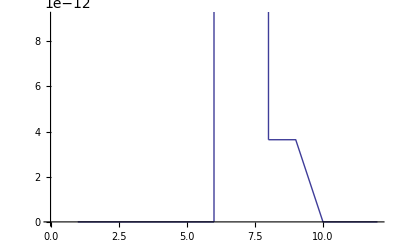

```mathematica
ListPlot[bat,Joined->True]
```

```mathematica
bat
```

{0.,0.,0.,0.,0.,0.,1000.,3.63798×10^-12,3.63798×10^-12,0.,0.,0.}

```mathematica
bat
```

{0.,0.,0.,0.}